```mathematica
Clear["`*"]
```

# Final Exam

## Spencer Lyon

## Part 1: OLS Estimation

```mathematica
SetDirectory["/Users/spencerlyon2/Desktop"];
data = Import["gmm_data.xlsx"];
```

```mathematica
{s1b1, s1b2, s1b3, s2b1, s2b2, s2b3, rmark, rf} = newData=Rest[Transpose[Rest[data[[1]]]]];
```

```mathematica
r1 = s1b1Excess = s1b1-rf;
r2 = s1b2Excess = s1b2-rf;
r3 = s1b3Excess = s1b3-rf;
r4 = s2b1Excess = s2b1-rf;
r5 = s2b2Excess = s2b2-rf;
r6 = s2b3Excess = s2b3-rf;
rm= marketExcess = rmark-rf;
excessList = {s1b1Excess,s1b2Excess,s1b3Excess,s2b1Excess,s2b2Excess,s2b3Excess,marketExcess};
n = Length[r1];means = Mean[#]&/@excessList[[1;;6]];
```

```mathematica
lms = {lm1,lm2,lm3,lm4,lm5,lm6}=Table[LinearModelFit[Transpose[{marketExcess,excessList[[i]]}],β,β],{i,1,6}];
βs =Table[lms[[i]]["BestFitParameters"][[2]],{i,1,6}];
λlm = LinearModelFit[Transpose[{βs,means}],λ,λ,IncludeConstantBasis->False];
AppendTo[lms,λlm];
λ1  = λlm["BestFitParameters"][[1]];
```

```mathematica
info = "ParameterTable";
Table[Print["OLS Regression info for data set " <>ToString[i]<>"   ",lms[[i]][info]],{i,1,Length[lms],1}]
```

OLS Regression info for data set 1    | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0016833 | 0.00133222 | -1.26353 | 0.206871
β | 1.33919 | 0.0293649 | 45.605 | 7.61481×10^-201

OLS Regression info for data set 2    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0034237 | 0.00102606 | 3.33674 | 0.000898019
β | 1.06817 | 0.0226165 | 47.2298 | 3.33051×10^-208

OLS Regression info for data set 3    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00507915 | 0.00119558 | 4.24827 | 0.0000248299
β | 1.05665 | 0.026353 | 40.0959 | 7.93759×10^-175

OLS Regression info for data set 4    | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.000311309 | 0.000480174 | -0.648325 | 0.517013
β | 1.00764 | 0.010584 | 95.2038 | 8.21062324022×10^-374

OLS Regression info for data set 5    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000969196 | 0.000626326 | 1.54743 | 0.122266
β | 0.902066 | 0.0138055 | 65.3411 | 2.95874×10^-281

OLS Regression info for data set 6    | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00223331 | 0.000907931 | 2.45978 | 0.0141721
β | 0.911814 | 0.0200126 | 45.5619 | 1.19903×10^-200

OLS Regression info for data set 7    | Estimate | Standard Error | t-Statistic | P-Value
λ | 0.00592887 | 0.000996231 | 5.9513 | 0.00191466

{Null,Null,Null,Null,Null,Null,Null}

Note that in the above output, data set 7 really mens the 2nd half of the two step process where we estimate λ.
Also note that where 1 appears in the tables, the row represents the statistics for the constant term α_i in the regresion.

```mathematica
smlPlot = Plot[λ1*β,{β,0,1.5},PlotRange->{-.005,.0125},PlotStyle->{Brown,Thick}];
pointsPlot = ListPlot[{
{{βs[[1]],Mean[r1]}},
{{βs[[2]],Mean[r2]}},
{{βs[[3]],Mean[r3]}},
{{βs[[4]],Mean[r4]}},
{{βs[[5]],Mean[r5]}},
{{βs[[6]],Mean[r6]}}
},PlotMarkers->{"s1b1","s1b2","s1b3","s2b1","s2b2","s2b3"},PlotRange->{{0,1.5},{-.005,.01}}];
```

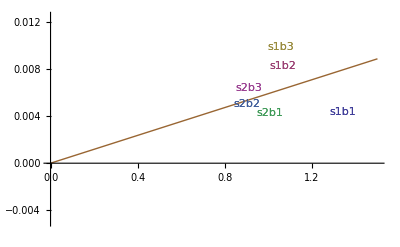

```mathematica
Show[smlPlot,pointsPlot]
```

```mathematica
means
```

{0.00438754,0.00826597,0.00986917,0.00425655,0.00505847,0.00636677}

```mathematica
StandardDeviation[#]&/@{r1,r2,r3,r4,r5,r6}
```

{0.0689817,0.0545907,0.0562422,0.0470629,0.0436291,0.0469779}

## Part2: GMM Estimation: No Serial Correlation

### The Code

### GMM Results (Parameter Estimates and Standard Errors) These are not Correct! Just the last output the computer gave.

Parameter | Estimate | SE
α_1 | -0.0029 | 0.0020
α_2 | 0.0013 | 0.0015
α_3 | 0.0016 | 0.0019
α_4 | 0.0027 | 0.0012
α_5 | -0.0009 | 0.0013
α_6 | -0.0022 | 0.0017
β_1 | 1.3415 | 0.0316
β_2 | 1.0839 | 0.0327
β_3 | 1.0765 | 0.0384
β_4 | 0.9981 | 0.0151
β_5 | 0.9155 | 0.0188
β_6 | 0.9360 | 0.0305
λ | 0.0045 | 0.0019

```mathematica
gmmSMLPlot = Plot[0.0045*β,{β,0,1.5},PlotRange->{-.005,.0125},PlotStyle->{Brown,Thick}];
pointsPlotGmm = ListPlot[{
{{1.3415,Mean[r1]}},
{{1.0839,Mean[r2]}},
{{1.0765,Mean[r3]}},
{{0.9981,Mean[r4]}},
{{0.9155,Mean[r5]}},
{{0.9360,Mean[r6]}}
},PlotMarkers->{"s1b1","s1b2","s1b3","s2b1","s2b2","s2b3"},PlotRange->{{0,1.5},{-.005,.01}}];
```

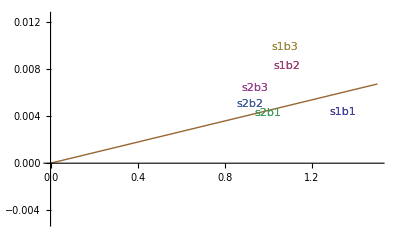

```mathematica
Show[gmmSMLPlot, pointsPlotGmm]
```

Although I didn’t get convergence, if you compare this plot to the one obtained through OLS you will see that they are very close. This is another evidence that the process in the GMM code is solid, the computer is just struggling with convergence.

```mathematica
pValueStandard = 1-CDF[ChiSquareDistribution[5],0.999999999999978];
Print["The j-statistic ~ χ^2 (5) was 0.999999999999978 and that has an associated p-value of ", ToString[pValueStandard]]
```

The j-statistic ~ χ^2 (5) was 0.999999999999978 and that has an associated p-value of 0.962566

## Part 3: GMM Estimation with Newey Standard Errors

### The Code

### The Results

Parameter | Estimate | SE
α_1 | -0.0043 | 0.0061
α_2 | 0.0054 | 0.0041
α_3 | 0.0084 | 0.0044
α_4 | -0.0045 | 0.0058
α_5 | 0.0025 | 0.0064
α_6 | 0.0054 | 0.0058
β_1 | 1.3612 | 0.0236
β_2 | 1.0726 | 0.0184
β_3 | 1.0553 | 0.0165
β_4 | 1.0237 | 0.0110
β_5 | 0.8836 | 0.0106
β_6 | 0.8866 | 0.0100
λ | 0.0069 | 0.0145

```mathematica
pValueStandard = 1-CDF[ChiSquareDistribution[5],0.167330676504051];
Print["The j-statistic ~ χ^2 (5) was 0.999999999999978 and that has an associated p-value of ", ToString[pValueStandard]]
```

The j-statistic ~ χ^2 (5) was 0.999999999999978 and that has an associated p-value of 0.999426

## Part 4: Discussion

### 4a.)

The main reason there are differences between my 2-stage OLS and GMM estimates for the α’s and β’s is that the GMM code in MatLab never quite converged. To remedy this I would have to provide my program with more sophistocated measures of the derivatives for the objective function. 

Another possible explanation is that 2sls is consistent, but biased whereas GMM is both consistent and unbiased. This means that for convergent solutions, the GMM results should be closer to the actual values than the the OLS estimates will be.

### 4b.)

The standard errors were different. One reason for this was that the standard “iid” GMM estimation makes the assumption that there is no serial correlation in the data. With time series this is highly unlikely. The newey procedure, however, allows for autocorrelative effects up to a certain lag. In this example that lag was set to 5. 

We would expect the standard errors to be smaller with the Newey case because when computing the S matrix, the newey procedure includes the iid case and additional factors. This leads to a larger S matrix in the newey case than that in the iid one. When computing the standard errors we take the inverse of the S matrix and the inverse of a matrix decreases as the size of its elements increase. We see this result hold true for the β’s, but not as much for the α’s.